```mathematica
P[k_,n_,p_]:=n!/(n-k)!/k!*p^k*(1-p)^(n-k)
```

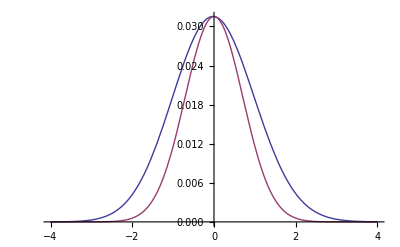

```mathematica
Plot[ {R[z,1000,0.2],Exp[-z^2]*R[0,1000,0.2]},{z,-4,4}, PlotRange->All]
```

```mathematica
R[z_,n_,p_]:=P[z*Sqrt[p*(1-p)*n]+n*p,n,p];
```

```mathematica
Log[R[z,n,p]]
```

Log[((1-p)^(n-n p-√(n (1-p) p) z) p^(n p+√(n (1-p) p) z) n!)/((n-n p-√(n (1-p) p) z)! (n p+√(n (1-p) p) z)!)]

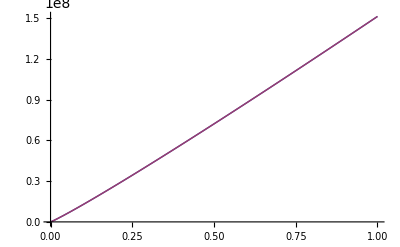

```mathematica
Plot[{Log[n!],n*(Log[n]-1)},{n,1,10000000}, PlotRange->All]
```

```mathematica
f[n_]:=n*(Log[n]-1)
```

```mathematica
Log[(1-p)^(n-n p-√(n (1-p) p) z) p^(n p+√(n (1-p) p) z)]+f[n]-f[n-n p-√(n (1-p) p) z]-f[n p+√(n (1-p) p) z]
```

n (-1+Log[n])+Log[(1-p)^(n-n p-√(n (1-p) p) z) p^(n p+√(n (1-p) p) z)]-(n-n p-√(n (1-p) p) z) (-1+Log[n-n p-√(n (1-p) p) z])-(n p+√(n (1-p) p) z) (-1+Log[n p+√(n (1-p) p) z])

```mathematica
Limit[%,n->Infinity]
```

$Aborted

```mathematica
Exp[Log[Pi]]
```

π